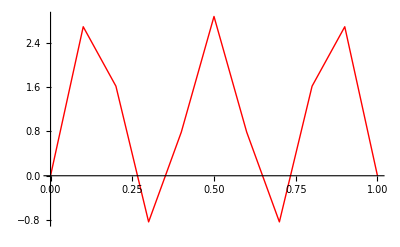

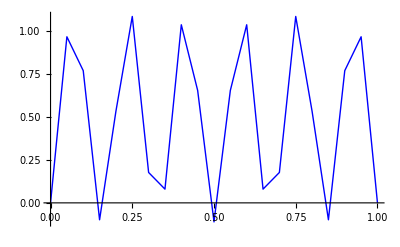

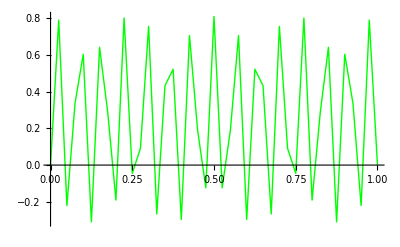

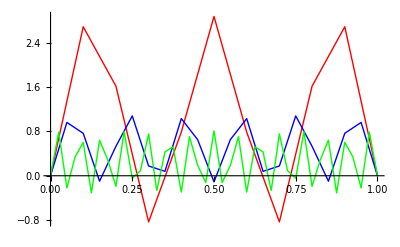

Показник збіжності  2.32255

Кількість ітерацій | Норма | Похибка | Відносна похибка
10 | 3.9601+0.111343 ⅈ | 0 | 0
20 | 0.373922+0.000508108 ⅈ | 25.444+1.80299 ⅈ | 6805.29+472.936 ⅈ
40 | 0.236392+0.013723 ⅈ | 5.5845+1.17873 ⅈ | 2383.3+360.278 ⅈ

```mathematica
(* Need to reach form A*c = B, where A = Mat *)
MyFunc = Function[{n,mu,be,de,fu},
(*main variables*)
(*
n = 20;
mu = 5;
be =-10;
de = 10;
fu = 10000;*)

INF = 1000000000;
myN =n+1;
h = 1/n;
(*preparing x[i]*)
xi = {};
start=0;
Do[
xi =AppendTo[xi,start];
start = start + h;
,{i,myN+1}];

(*preparing matrix*)
Mat = {{}};
tmp = {};
Do[tmp = AppendTo[tmp, 0], {i,myN}];
Do[Mat = AppendTo[Mat, tmp], {i,myN}];
Mat = Delete[Mat, {1}];


(*fill main diagonal*)
Mat[[myN]][[myN]] =Mat[[1]][[1]]=INF;
Do[
val = 0;
val = val + Integrate[mu*(1/h^2), {x, xi[[i-1]], xi[[i+1]]} ];
val = val + Integrate[(x-xi[[i-1]])*be/h^2, {x, xi[[i-1]], xi[[i]]} ] +Integrate[(xi[[i+1]]-x)*be*(-1/h^2), {x, xi[[i]], xi[[i+1]]} ];
val = val + Integrate[de*(x-xi[[i-1]])^2/h^2, {x, xi[[i-1]], xi[[i]]} ]+
Integrate[de*(xi[[i+1]]-x)^2/h^2, {x, xi[[i]], xi[[i+1]]} ];

Mat[[i]][[i]] = val;
, {i,2,myN-1,1}];


(*fill upper diagonal*)
Do[
val = 0;
val = val + Integrate[mu*(-1/h^2), {x, xi[[i]], xi[[i+1]]} ];
val = val + Integrate[be*(x-xi[[i]])*(-1/h^2), {x, xi[[i]], xi[[i+1]]} ];
val = val + Integrate[de*(xi[[i+1]]-x)*(x-xi[[i]])/h^2, {x, xi[[i]], xi[[i+1]]} ];
Mat[[i]][[i+1]] = val;
, {i,1,myN-1,1}];


(*fill bottom diagonal*)
Do[
val = 0;
val = val + Integrate[mu*(-1/h^2), {x, xi[[i]], xi[[i+1]]} ];
val = val + Integrate[be*(xi[[i+1]]-x)/(h^2), {x, xi[[i]], xi[[i+1]]} ];
val = val + Integrate[de*(xi[[i+1]]-x)*(x-xi[[i]])/h^2, {x, xi[[i]], xi[[i+1]]} ];
Mat[[i+1]][[i]] = val;
, {i,1,myN-1,1}];


(*prepare B*)
B = {};
B = AppendTo[B, Integrate[fu*(xi[[2]]-x)/h, {x,xi[[1]],xi[[2]]}] ];
Do[
val = 0;
val = val + Integrate[fu*(x-xi[[i-1]])/h, {x,xi[[i-1]],xi[[i]]}];
val = val + Integrate[fu*(xi[[i+1]]-x)/h, {x,xi[[i]],xi[[i+1]]}];
B = AppendTo[B, val];
, {i,2,myN-1,1}];
B = AppendTo[B, Integrate[fu*(x-xi[[myN-1]])/h, {x,xi[[myN-1]],xi[[myN]]}] ];

(*solve equation progonka*)
res = Array[0,{myN}];
A = Mat;
temp = 0;
A[[1]][[2]]  = A[[1]][[2]] /A[[1]][[1]];
B[[1]] =- B[[1]]/A[[1]][[1]];
For   [i=2, i<myN, i++,
 temp = 1/ (A[[i]][[i]]- A[[i-1]][[i]]*A[[i]][[i-1]] );
A[[i]][[i+1]] = A[[i]][[i+1]]*temp;
B[[i]] =(B[[i]]- B[[i-1]]*A[[i]][[i-1]] )*temp; 
]

res[[myN]] = -(A[[myN]][[myN-1]]*B[[myN-1]]- B[[myN]])/(A[[myN]][[myN]]- A[[myN]][[myN-1]]*A[[myN-1]][[myN]]);
For[i= myN-1, i>0, i--,
res[[i]] = B[[i]]- A[[i]][[i+1]]*res[[i+1]];
]



   
(*res = LinearSolve[A,B];*)
Dots = {{}};
Do[
Dots = AppendTo[Dots,{xi[[i]], res[[i]]}]; ,{i,myN}];

Dots = Delete[Dots,{1}];

Return[Dots];
];

(* Processing Data *)
n = 10;
mu = 5;
be =1000;
de = 10;
fu = 10000;
X = MyFunc[n,mu,be,de,fu][[1]];
N[X];
g1 =ListLinePlot[X,PlotStyle -> Red]
X2 = MyFunc[(2*n),mu,be,de,fu][[1]];
N[X2];
g2 =ListLinePlot[X2,PlotStyle -> Blue]
X4 = MyFunc[(4*n),mu,be,de,fu][[1]];
N[X4];
g3 = ListLinePlot[X4,PlotStyle ->Green]
Show[g1,g2,g3]
p =0;
sum =0;
Do[
sum = sum +N[(X[[i,2]]-X2[[(2*i-1),2]])/(X2[[(2*i-1),2]]-X4[[(4*i-3),2]])],
{i,n+1}
]


p = Log[2, sum/(n+1)];
Print ["Показник збіжності  ",p];
TabulaCWM = {{}};
nX = 0;
nX2 = 0;
nX4 = 0;
pX =0;
pX2 =0;
pX4 = 0;
pX3 =0;
vX =0;
vX2 = 0;
vX4 = 0;
Do[
pX2 = pX2 + Chop[Integrate[(X[[i,2]]-X2[[(2*i-1),2]])^p, {x, 0, 1} ], 10^-11];
pX4 = pX4 + Chop[Integrate[(X[[i,2]]-X4[[(4*i-3),2]])^p, {x, 0, 1} ],10^-12];
pX3 = pX3 + Chop[Integrate[(X2[[(2*i-1),2]]-X4[[(4*i-3),2]])^p, {x, 0, 1} ],10^-12];

nX = nX + N[Integrate[X[[i,2]]^p, {x, 0, 1} ]/n];
nX2 = nX2 + N[Integrate[X2[[(2*i-1),2]]^p, {x, 0, 1} ]/n];
nX4 = nX4 + N[Integrate[X4[[(4*i-3),2]]^p, {x, 0, 1} ]/n],
{i,n+1}
]
vX2 = Chop[(pX2/nX2),10^-15]*100;
vX4 = Chop[(pX3/nX4),10^-15]*100;
TabulaCWM = AppendTo[TabulaCWM,{n, nX, pX,vX}];
TabulaCWM = AppendTo[TabulaCWM,{2*n, nX2, pX2,vX2}];
TabulaCWM = AppendTo[TabulaCWM,{4*n, nX4, pX3,vX4}];


TabulaCWM = Delete[TabulaCWM, {1}];
 Print[TableForm[TabulaCWM,TableHeadings->{None,{"Кількість ітерацій","Норма", "Похибка","Відносна похибка"}}]];
```